```mathematica
(* Holographie *)
(* Interférences entre deux ondes sphériques *)
```

```mathematica
lambda=256000 (* nm, longueur d'onde de production des hologrammes 640 nm *)
```

256000

```mathematica
U[x_,y_,z_]:=Exp[2*I*Pi*Sqrt[x^2+y^2+z^2]*10^6/lambda]/Sqrt[x^2+y^2+z^2] (* onde sphérique source en 0 *)
```

```mathematica
(* Superposition des ondes de deux sources en (0,0,0) et en (xB,0,0) dans le plan défini par z=zE *)
```

```mathematica
xB=11.3 (* mm *)
```

11.3

```mathematica
zE=-58 (* mm *)
```

-58

```mathematica
A[x_,y_]:=U[x,y,zE]+U[x-xB,y,zE]
```

```mathematica
(* Intensité *)
Intensity[x_,y_]:=A[x,y]*Conjugate[A[x,y]]
```

```mathematica
p=DensityPlot[Intensity[x,y],{x,-25.,25.},{y,-25.,25.},PlotPoints->500]
```

-Graphics-

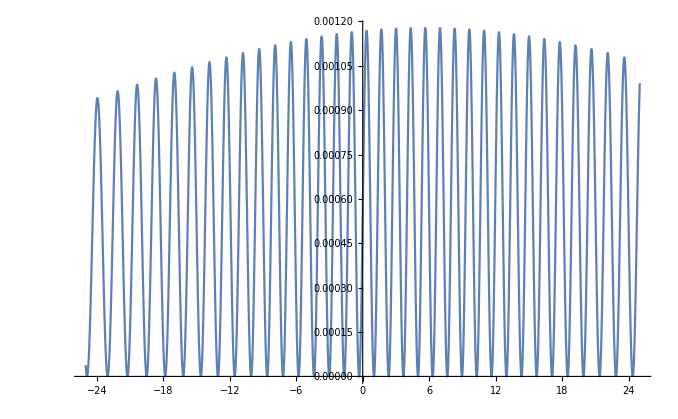

```mathematica
Plot[Intensity[x,0],{x,-25.,25.},PlotPoints->500]
```

```mathematica
Export["/Users/jneveu/Documents/LSST/Calibration/CTIOAnaJun2017/common_tools/pictures/hologram_lambdaratio400.png",p]
```

/Users/jneveu/Documents/LSST/Calibration/CTIOAnaJun2017/common_tools/pictures/hologram_lambdaratio400.png

```mathematica
Export["/Users/jneveu/Documents/LSST/Calibration/CTIOAnaJun2017/common_tools/pictures/hologram_lambdaratio400.txt",Table[Table[Re[Intensity[x,y]],{x,-25.,25.,0.1}],{y,-25.,25.,0.1}],"Table"]
```

/Users/jneveu/Documents/LSST/Calibration/CTIOAnaJun2017/common_tools/pictures/hologram_lambdaratio400.txt